# Lab 1: Cavendish Experiment

## Import the Data

```mathematica
(* Set path to data files *)
path="/Users/jackson/PHY64/lab1/data/";
```

```mathematica
dataDriven=Import[StringJoin[path,"driven.txt"],"Data"];
dataTrial1Clockwise=Import[StringJoin[path,"trial1_clockwise.txt"],"Data"];
dataTrial1CounterClockwise=Import[StringJoin[path,"trial1_counterclockwise.txt"],"Data"];
dataTrial2CounterClockwise=Import[StringJoin[path,"trial2_counterclockwise.txt"],"Data"];
dataTrial2Clockwise=Import[StringJoin[path,"trial2_clockwise.txt"],"Data"];
```

## Plot the Data

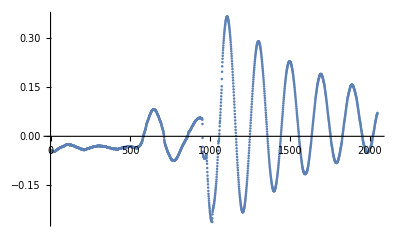

```mathematica
ListPlot[dataDriven]
```

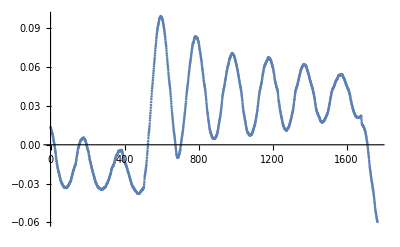

```mathematica
ListPlot[dataTrial1CounterClockwise]
```

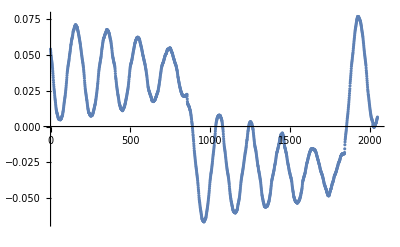

```mathematica
ListPlot[dataTrial1Clockwise]
```

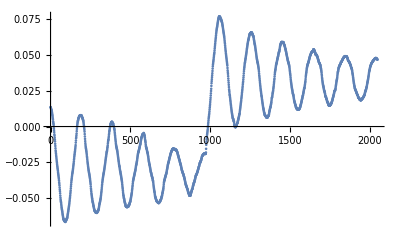

```mathematica
ListPlot[dataTrial2CounterClockwise]
```

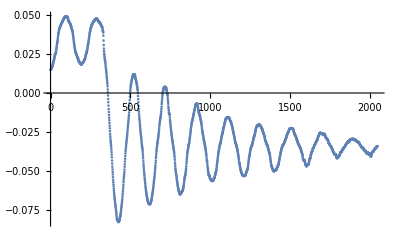

```mathematica
ListPlot[dataTrial2Clockwise]
```

## Trim the Data

```mathematica
(* Next we will cut the data sets to only incorporate the relevant sections of data *)
```

```mathematica
(* Just a test *)
```

```mathematica
dataDriven=Drop[dataDriven,975];
dataTrial1CounterClockwise=Part[dataTrial1CounterClockwise,500;;1650];
dataTrial1Clockwise=Part[dataTrial1Clockwise,855;;1800];
dataTrial2CounterClockwise=Drop[dataTrial2CounterClockwise,970];
dataTrial2Clockwise=Drop[dataTrial2Clockwise,350];
```

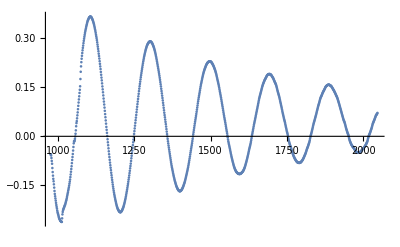

```mathematica
ListPlot[dataDriven]
```

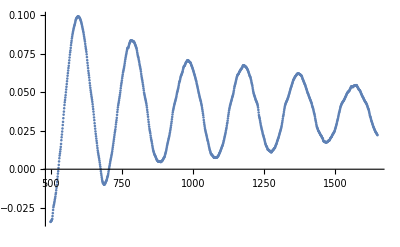

```mathematica
ListPlot[dataTrial1CounterClockwise]
```

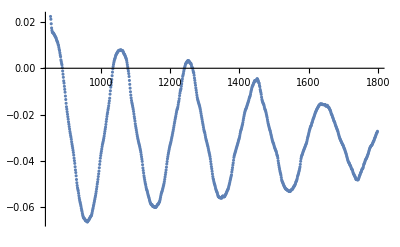

```mathematica
ListPlot[dataTrial1Clockwise]
```

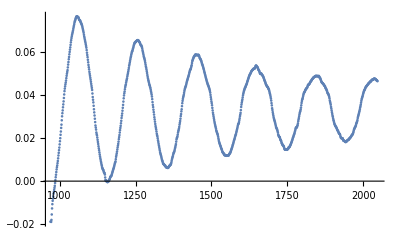

```mathematica
ListPlot[dataTrial2CounterClockwise]
```

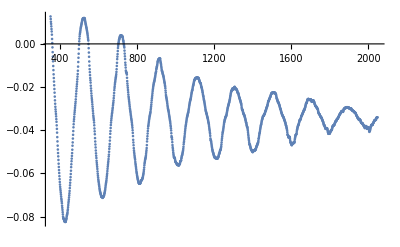

```mathematica
ListPlot[dataTrial2Clockwise]
```

## Fit the Data

```mathematica
(* First fit the driven data to acquire a better guess for the period *)
```

```mathematica
DrivenFit=NonlinearModelFit[dataDriven,A E^(-β t)Cos[ω(t-dataDriven[[1]][[1]]) + ϕ]-δ,{{β,.01},{A,.4},{ω,.035},ϕ,{δ,.04}},t]
```

FittedModel[0.0491749+1.06449 ⅇ^(-«21» t) Cos[1.99826+0.0322125 (-975.+t)]]

```mathematica
DrivenFit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.00116614 | 9.42069×10^-6 | 123.785 | 1.16021755786×10^-635
A | 1.06449 | 0.0132969 | 80.0556 | 1.29054019467×10^-453
ω | 0.0322125 | 9.61169×10^-6 | 3351.39 | 4.80746203558×10^-2150
ϕ | 1.99826 | 0.00419819 | 475.981 | 7.75239108953×10^-1246
δ | -0.0491749 | 0.000374336 | -131.365 | 1.56125276671×10^-661

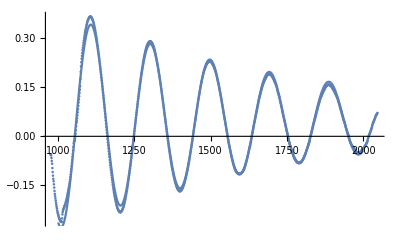

```mathematica
Show[ListPlot[dataDriven],Plot[DrivenFit[x],{x,1000,2000}]]
```

```mathematica
(* Trial 1 *)
```

```mathematica
CounterClockwise1Fit=NonlinearModelFit[dataTrial1CounterClockwise,A E^(-β t)Cos[ω(t-dataTrial1CounterClockwise[[1]][[1]]) + ϕ]-δ,{{β,.001},{A,.05},{ω,.0322},ϕ,{δ,-.04}},t]
```

FittedModel[0.0393352+0.119649 ⅇ^(-«22» t) Cos[3.14894+0.0324038 (-499.+t)]]

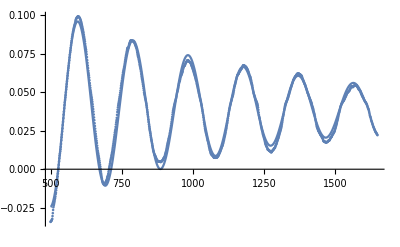

```mathematica
Show[ListPlot[dataTrial1CounterClockwise],Plot[CounterClockwise1Fit[x],{x,dataTrial1CounterClockwise[[1]][[1]],1600}]]
```

```mathematica
Clockwise1Fit=NonlinearModelFit[dataTrial1Clockwise,A E^(-β t)Cos[ω(t-dataTrial1Clockwise[[1]][[1]]) + ϕ]-δ,{{β,.001},{A,.05},{ω,.0322},ϕ,{δ,-.04}},t]
```

FittedModel[-0.0297304+0.115655 ⅇ^(-«22» t) Cos[0.284371-0.0322222 (-854.+t)]]

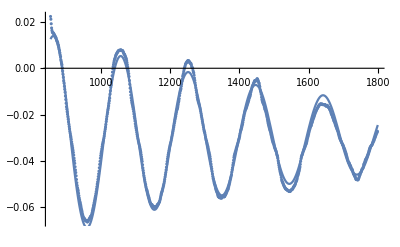

```mathematica
Show[ListPlot[dataTrial1Clockwise],Plot[Clockwise1Fit[x],{x,dataTrial1Clockwise[[1]][[1]],1800}]]
```

```mathematica
(* Trial 2 *)
```

```mathematica
CounterClockwise2Fit=NonlinearModelFit[dataTrial2CounterClockwise,A E^(-β t)Cos[ω(t-dataTrial2CounterClockwise[[1]][[1]]) + ϕ]-δ,{{β,.001},{A,.05},{ω,.0322},ϕ,{δ,-.04}},t]
```

FittedModel[0.0343609+0.144733 ⅇ^(-«22» t) Cos[3.32821+0.0321205 (-970.+t)]]

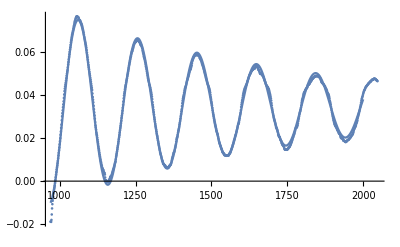

```mathematica
Show[ListPlot[dataTrial2CounterClockwise],Plot[CounterClockwise2Fit[x],{x,dataTrial2CounterClockwise[[1]][[1]],2000}]]
```

```mathematica
Clockwise2Fit=NonlinearModelFit[dataTrial2Clockwise,A E^(-β t)Cos[ω(t-dataTrial2Clockwise[[1]][[1]]) + ϕ]-δ,{{β,.001},{A,.05},{ω,.0322},ϕ,{δ,-.04}},t]
```

FittedModel[-0.0337269+0.0904922 ⅇ^(-«22» t) Cos[0.712815+0.0320778 (-350.+t)]]

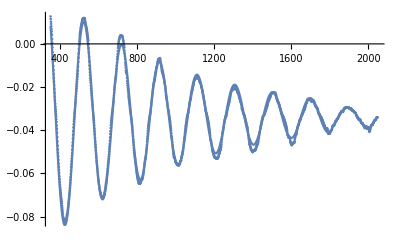

```mathematica
Show[ListPlot[dataTrial2Clockwise],Plot[Clockwise2Fit[x],{x,dataTrial2Clockwise[[1]][[1]],1800}]]
```

```mathematica
(* Calculate the difference DV in transducer voltage for equilibrium positions *)
```

```mathematica
Clockwise1δ=Clockwise1Fit["BestFitParameters"][[5]][[2]]
```

0.0297304

```mathematica
CounterClockwise1δ=CounterClockwise1Fit["BestFitParameters"][[5]][[2]]
```

-0.0393352

```mathematica
Clockwise2δ=Clockwise2Fit["BestFitParameters"][[5]][[2]]
```

0.0337269

```mathematica
CounterClockwise2δ=CounterClockwise2Fit["BestFitParameters"][[5]][[2]]
```

-0.0343609

```mathematica
DV1=Abs[Clockwise1δ-CounterClockwise1δ]
```

0.0690656

```mathematica
DV2=Abs[Clockwise2δ-CounterClockwise2δ]
```

0.0680878

```mathematica
DVAverage=(DV1+DV2)/2
```

0.0685767

```mathematica
(* Calculate the period *)
```

```mathematica
Drivenω=DrivenFit["BestFitParameters"][[3]][[2]]
```

0.0322125

```mathematica
Clockwise1ω=Clockwise1Fit["BestFitParameters"][[3]][[2]]
```

0.0322222

```mathematica
CounterClockwise1ω=CounterClockwise1Fit["BestFitParameters"][[3]][[2]]
```

0.0324038

```mathematica
Clockwise2ω=Clockwise2Fit["BestFitParameters"][[3]][[2]]
```

0.0320778

```mathematica
CounterClockwise2ω=CounterClockwise2Fit["BestFitParameters"][[3]][[2]]
```

0.0321205

```mathematica
ωData={Drivenω,Clockwise1ω,CounterClockwise1ω,Clockwise2ω,CounterClockwise2ω}
```

{0.0322125,0.0322222,0.0324038,0.0320778,0.0321205}

```mathematica
ωAverage=Mean[ωData]
```

0.0322074

```mathematica
Period=2Pi/ωAverage
```

195.085

### Calibrating the Apparatus

```mathematica
localMax[data_]:=Block[{},
ret=Reap[
For[i=80,i≤Length[data]-1,i++,
If[data⟦i,2⟧>data⟦i-1,2⟧&&data⟦i,2⟧>data⟦i+1,2⟧,
Sow[data⟦i,2⟧],
Continue[]
];
];
];
Return[ret⟦2,1⟧]
]
```

```mathematica
drivenMax=localMax[dataDriven]
```

{0.36678,0.2903,0.22912,0.19049,0.15786}

```mathematica
localMin[data_]:=Block[{},
ret=Reap[
For[i=80,i≤Length[data]-1,i++,
If[data⟦i,2⟧<data⟦i-1,2⟧&&data⟦i,2⟧<data⟦i+1,2⟧,
Sow[data⟦i,2⟧],
Continue[]
];
];
];
Return[ret⟦2,1⟧]
]
```

```mathematica
drivenMin=localMin[dataDriven]
```

{-0.2324,-0.16795,-0.11524,-0.08129,-0.05009}

```mathematica
L=583.1+3.52/2
```

584.86

```mathematica
θMax={ArcTan[L,14.4]/2,ArcTan[L,16.8]/2,ArcTan[L,18.5]/2,ArcTan[L,19.8]/2,ArcTan[L,20.0]/2}
```

{0.0123082,0.0143585,0.0158105,0.0169207,0.0170914}

```mathematica
θMin={ArcTan[L,32.5]/2,ArcTan[L,30.8]/2,ArcTan[L,29.2]/2,ArcTan[L,28.1]/2,ArcTan[L,27.1]/2}
```

{0.0277559,0.0263068,0.0249425,0.0240044,0.0231514}

```mathematica
calibrationListMax=Table[{θMax⟦i⟧,drivenMax⟦i⟧},{i,1,5}]
```

{{0.0123082,0.36678},{0.0143585,0.2903},{0.0158105,0.22912},{0.0169207,0.19049},{0.0170914,0.15786}}

```mathematica
calibrationListMin=Table[{θMin⟦i⟧,drivenMin⟦i⟧},{i,1,5}]
```

{{0.0277559,-0.2324},{0.0263068,-0.16795},{0.0249425,-0.11524},{0.0240044,-0.08129},{0.0231514,-0.05009}}

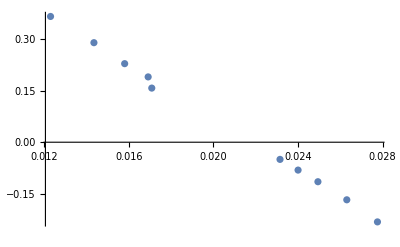

```mathematica
ListPlot[calibrationList]
```

```mathematica
calibrationList=Join[calibrationListMax,calibrationListMin]
```

{{0.0123082,0.36678},{0.0143585,0.2903},{0.0158105,0.22912},{0.0169207,0.19049},{0.0170914,0.15786},{0.0277559,-0.2324},{0.0263068,-0.16795},{0.0249425,-0.11524},{0.0240044,-0.08129},{0.0231514,-0.05009}}

```mathematica
calibrationFit=LinearModelFit[calibrationList,x ,x]
```

FittedModel[0.831975-38.1552 x]

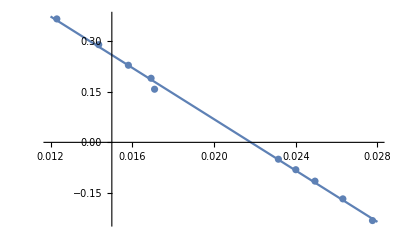

```mathematica
Show[Plot[calibrationFit[x],{x,.012,.028}],ListPlot[calibrationList]]
```

```mathematica
K=calibrationFit["BestFitParameters"]⟦2⟧
```

-38.1552

```mathematica
const=calibrationFit["BestFitParameters"]⟦1⟧
```

0.831975

## Moment of Intertion of the Rod

```mathematica
(* masses are in kilograms,lengths are in meters *)
```

```mathematica
(* mass of sphere *)
```

```mathematica
m=0.0145;
```

```mathematica
(* mass of rod *)
```

```mathematica
mRod=0.00717;
```

```mathematica
(* radius of sphere *)
```

```mathematica
r=0.0135/2;
```

```mathematica
(* distance from sphere to rod center *)
```

```mathematica
d=0.0667;
```

```mathematica
(* mass density *)
```

```mathematica
σ=mRod/(2d)
```

0.0537481

```mathematica
(* width of the rod *)
```

```mathematica
w=0.0127;
```

```mathematica
(* Moment of Inertia *)
```

```mathematica
ISystem=4/5 m r^2+2m d^2+2d σ(w^2+4 d^2)/12
```

0.000140276

## Calculating the Torsional Constant

```mathematica
λ=ISystem((2Pi)/Period)^2
```

1.4551×10^-7

## Calculating the Torque